# ChemicalSpaceNetwork

A function that generates a chemical space network from molecule data

## Definition

```mathematica
Needs["WolframChemistry`MoleculeFingerprints`"];
validSmilesQ[smile_String] :=
    MatchQ[Quiet[Molecule[smile]], Except[$Failed]]
moleculeListQ[list_] := AllTrue[list, MoleculeQ]
cleanDataset[data_Dataset] :=
    data[Select[StringFreeQ[#Smiles, "."]&]]
SetAttributes[makeID, Listable];
makeID[prefix_String, number_Integer?Positive, maxDigits_Integer?Positive] :=prefix <> IntegerString[number, 10, Max[maxDigits, Ceiling[Log10[number]]]]
Options[generateDataset]={"FieldSeparator"->";"};
generateDataset[file_,OptionsPattern[]] := Module[{data, dataset, idKey, ids},
  data = Import[file, "Table", "FieldSeparators" -> OptionValue["FieldSeparator"], "RepeatedSeparators" -> False];
  dataset = Dataset[AssociationThread[First[data] -> #]& /@ Rest[data]];
  idKey = SelectFirst[Keys[First[dataset]] // Normal, StringMatchQ[RegularExpression["(?i).*ID.*"]]];
  ids = If[MissingQ[idKey], makeID["ID", Range[Length[dataset]], Ceiling[Log10[Length[dataset]]]], Normal@dataset[All, idKey]];
  AssociationThread[ids, Normal@dataset[All, {"Smiles"}]] // Dataset // cleanDataset
]
Options[generateDatasetBio]={"FieldSeparator"->";"};
generateDatasetBio[file_,biotype_,OptionsPattern[]] := Module[{data, dataset, idKey, ids},
  data = Import[file, "Table", "FieldSeparators" -> OptionValue["FieldSeparator"], "RepeatedSeparators" -> False];
  dataset = Dataset[AssociationThread[First[data] -> #]& /@ Rest[data]];
  idKey = SelectFirst[Keys[First[dataset]] // Normal, StringMatchQ[RegularExpression["(?i).*ID.*"]]];
  ids = If[MissingQ[idKey], makeID["ID", Range[Length[dataset]], Ceiling[Log10[Length[dataset]]]], Normal@dataset[All, idKey]];
  dataset = AssociationThread[ids, Normal@dataset[All, {"Smiles", "Standard Value"}]] // Dataset;
  dataset = dataset[Select[NumericQ[#"Standard Value"]&]] // cleanDataset;
  dataset[All, {"Standard Value" -> (9 - Log10[#]&)}][All, KeyMap[# /. "Standard Value" -> biotype&]]
]
Options[assignFingerprintsList] = Join[{"Fingerprint" -> TopologicalFingerprint}, Options[TopologicalFingerprint],Options[generateDataset]];
assignFingerprintsList[molList_, OptionsPattern[]] :=
    Dataset[AssociationThread[{"Molecule", "Fingerprint"} -> #]& /@ Map[{#, OptionValue["Fingerprint"][#]}&, molList]]
Options[assignFingerprints] = Join[{"Fingerprint" -> TopologicalFingerprint}, Options[TopologicalFingerprint],Options[generateDataset]];
assignFingerprints[dataset_Dataset, opts : OptionsPattern[]] := dataset[All,
  With[{mol = Molecule[#"Smiles", IncludeHydrogens -> False]}, <|##,
    "Molecule" -> mol, "Fingerprint" -> OptionValue["Fingerprint"][mol]|>]&]
```

```mathematica
defaultBioToColor[bio_]:=Which[
bio<5,Darker@Red,
5<=bio<6,Red,
6<=bio<7,Orange,
7<=bio<8,Yellow,
8<=bio<9,Darker@Green,
9<=bio<10,LightBlue,
10<=bio,Blue,True,White]
Options[generateInput]=Join[{"BioData"->False,"BioType"->"pKi"},Options[assignFingerprintsList]];
generateInput[userInput_,opts:OptionsPattern[]]:=Module[{dataset},
dataset=Which[
StringQ[userInput]&&StringEndsQ[userInput,".csv"],If[TrueQ[OptionValue["BioData"]],generateDatasetBio[userInput,OptionValue["BioType"]],generateDataset[userInput]],
StringQ[userInput]&&StringEndsQ[userInput,".smi"],Import[userInput],
ListQ[userInput]&&moleculeListQ[userInput],userInput,
ListQ[userInput]&&validSmilesQ[First@userInput],Molecule/@userInput,
True,$Failed];
If[dataset===$Failed,Return[$Failed]];
If[ListQ[userInput],
assignFingerprintsList[dataset,"Fingerprint"->OptionValue["Fingerprint"]],
assignFingerprints[dataset,"Fingerprint"->OptionValue["Fingerprint"]]]
]
Options[generateGraphWithMols]=Join[Options[MoleculeDistance],{"Embedding"->"GravityEmbedding"}];
generateGraphWithMols[fingerprintData_Dataset,cutoff_,OptionsPattern[]]:=Module[{fingerprints,edges,graph},
fingerprints=KeyValueMap[{#1,#2["Fingerprint"]}&,fingerprintData]//Normal;
edges=ParallelMap[UndirectedEdge[Sequence@@First/@#]->N@*OptionValue["DistanceFunction"]@@Last/@#&,Subsets[fingerprints,{2}]]//Association;
graph=Select[edges,#<=cutoff&]//Keys//Graph[Tooltip[#,MoleculePlot[fingerprintData[#,"Molecule"]]]&/@Union@@List@@@#,#,GraphLayout->OptionValue["Embedding"]]&;
SetProperty[graph,EdgeWeight->Normal@Map[1-#&,edges]]
]
Options[generateGraph]=Join[Options[MoleculeDistance],{"Embedding"->"GravityEmbedding"}];
generateGraph[fingerprintData_Dataset,cutoff_,OptionsPattern[]]:=Module[{fingerprints,edges,graph},
fingerprints=KeyValueMap[{#1,#2["Fingerprint"]}&,fingerprintData]//Normal;
edges=ParallelMap[UndirectedEdge[Sequence@@First/@#]->N@*OptionValue["DistanceFunction"]@@Last/@#&,Subsets[fingerprints,{2}]]//Association;
graph=Select[edges,#<=cutoff&]//Keys//Graph[Tooltip/@Union@@List@@@#,#,GraphLayout->OptionValue["Embedding"]]&;
SetProperty[graph,EdgeWeight->Normal@Map[1-#&,edges]]
]
Options[chemicalSpaceNetwork]:=Join[{"Embed Molecules"->False},{"Coloring"->defaultBioToColor},Options[generateGraph],Options[generateInput]]
chemicalSpaceNetwork[userInput_,cutoff_,opts:OptionsPattern[]]:=Module[{fingerprints,vertices,style,graph,legend},
fingerprints=generateInput[userInput,"BioData"->OptionValue["BioData"],"BioType"->OptionValue["BioType"]];
graph=If[OptionValue["Embed Molecules"],generateGraphWithMols[fingerprints,cutoff],generateGraph[fingerprints,cutoff]];
If[OptionValue["BioData"],
vertices=VertexList[graph];
style=#->OptionValue["Coloring"][fingerprints[#,OptionValue["BioType"]]]&/@vertices;
legend=Row[{BarLegend[{OptionValue["Coloring"],{4,11}},6],Rotate["pKi",90Degree]}];
SetProperty[graph,VertexStyle->style]//Legended[#,legend]&,graph]
]
```

## Documentation

### Usage

ResourceFunction["ChemicalSpaceNetwork"][file.csv,cutoff]

Generatesachemicalspacegraphfromacsvfilecontaining"SMILES"strings with edges between vertices having similarity>=cutoff

ResourceFunction["ChemicalSpaceNetwork"][list,cutoff]

Generates a chemical space graph from a list of"SMILES"stringswith edges between vertices having similarity>=cutoff

ResourceFunction["ChemicalSpaceNetwork"][list,cutoff]

GeneratesachemicalspacegraphfromalistofMoleculeobjectswithedgesbetweenverticeshavingsimilarity>=cutoff

ResourceFunction["ChemicalSpaceNetwork"][file.smi,cutoff]

Generates a chemical space graph from a SMI file containing"SMILES"strings with edges between vertices having similarity>=cutoff

### Details & Options

A chemical space network is a graph 𝒢 of molecules. The set of vertices 𝒱(𝒢) is the set of molecules and the edges ℯ ϵ ℰ(𝒢) are generated from molecules with distance measures <= α. See Maggiora, G. M., & Bajorath, J. (2014). Chemical space networks: A powerful new paradigm for the description of chemical space. Journal of Computer-Aided Molecular Design, 28(8), 795–802. for more details.

The edge cutoff is a real number α between[0,1], all distance measures less than or equal to the cutoff generate an edge in the network

The function accepts the following inputs

.csv file | file formatted with each molecule having at least a SMILES string
.smi file | file in the SMILE format
list of Molecules[] | a list of Molecule objects
SMILE strings | a list of SMILE strings

#### Graph Computation Options

BioData | False | whether to include biological data as a graph coloring
Embedding | Gravity | the type of embedding used to render the final graph
Embed Molecules | False | Whether to embed Molecule plots into the graph vertices
Fingerprint | Topological | the fingerprint used to encode molecular features
BioType | pKi | the type of biological data expected
DistanceFunction | JaccardDissimilarity | the function that generates distances between features
Coloring | Automatic | the function used to sort biological data into colors

Biological data is currently represented as a column titled "Standard Value" for data. The inverse base 10 log is taken and passed using a defualt graph coloring scheme.

The options for the Fingerprint option derive from the MolecularFingerprints paclet and are

TopologicalFingerprint | Features based on paths
ExtendedConnectivityFingerprint | Features based on all atoms in a given "radius"
AtomPairFingerprint | Feature based on pairs of atoms and distances
MACCSKeyFingerprint | Predefined set of substrucutre keys
SubstructureKeyFingerprint | Use a custom set of molecule patterns
LayeredFingerprint | Alternate topological fingerprint using different graph hashing

The DistanceFunction option derives from the options for the MolecularDistance function in the MolecularFingerprints paclet and can be any valid DistanceFunction. The most common options are the default JaccardDissimilarity and the DiceDissimilarity. When fingerprints return count vectors, multi set versions of the DistanceFunctions are used.

## Examples

### Basic Examples

The generation of a simple chemical space network with biological data from a file "D5Activities.csv" that contains SMILES strings and IDs. The cutoff is set to 0.5

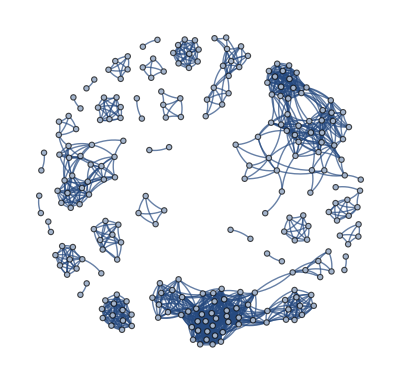

```mathematica
chemicalSpaceNetwork["/Users/joshuakhorsandi/Documents/Summer Research - 2023/WSS 2023/Chem Space - #225/ChemicalSpaceNetworks/ChemicalSpaceNetworks/Data/D5Activities.csv",0.5]
```

### Options

#### Bio Data

The same chemical network with "BioData" set to True and using the default vertex coloring scheme. The data set uses Ki as the biological data type:

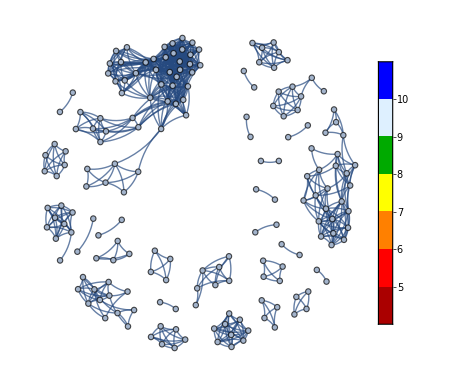

```mathematica
chemicalSpaceNetwork["/Users/joshuakhorsandi/Documents/Summer Research - 2023/WSS 2023/Chem Space - #225/ChemicalSpaceNetworks/ChemicalSpaceNetworks/Data/D5Activities.csv",0.5,"BioData"->True]
```

#### Embed Molecules

The same network with MoleculePlot objects embedded as tooltips

```mathematica
chemicalSpaceNetwork["/Users/joshuakhorsandi/Documents/Summer Research - 2023/WSS 2023/Chem Space - #225/ChemicalSpaceNetworks/ChemicalSpaceNetworks/Data/D5Activities.csv",0.5,"Embed Molecules"->True]
```

-Graphics-

### Possible Issues

#### BioData

"BioData"->True returns a Legended object without Annotations, apply First to return the regular colored Graph object

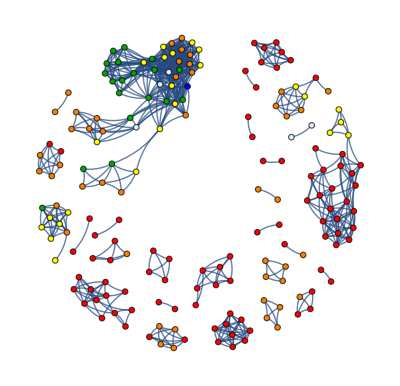

```mathematica
First@chemicalSpaceNetwork["/Users/joshuakhorsandi/Documents/Summer Research - 2023/WSS 2023/Chem Space - #225/ChemicalSpaceNetworks/ChemicalSpaceNetworks/Data/D5Activities.csv",0.5,"BioData"->True]
```

## Source & Additional Information

### Contributed By

Joshua Khorsandi

### Keywords

Chemistry,

Biology

Graphs

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Repository Tools
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction
 Wolfram Physics Project |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Just For Fun
 Machine Learning
 Programming Utilities
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics

### Related Symbols

SymbolName (documented Wolfram Language symbol)

### Related Resource Objects

MolecularFingerprints paclet

IGraph/M

### Source/Reference Citation

Source, reference or citation information

### Links

Link to other related material

### Tests

### Compatibility

#### Wolfram Language Version

13.0+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

## Author Notes

Additional information about limitations, issues, etc.

## Submission Notes

Additional information for the reviewer.